```mathematica
(* Podatki zob *)
αk=30°;
pk=9.52;
a=0.8567 pk;
f=0.6128 a;
L=1.86 pk;
h1=0.33 pk;
h2=0.7 pk;
h3=1.115 pk;

r0=28;
r1=2.6;
r2=5.5;
r3=1.2;
r4=14.3;
r5=1.8;

(* Podatki luknja *)
pch=9.518;
ro1=0.165 pch;
Hb=0.425 pch;
Hbc=0.415 pch;
```

```mathematica
{y0,t1A, t1B, t2B, t2C, t3C,t3D,t4D,t4E,t5E,t5F,t6F,t6G,t7G,t7H}
```

```mathematica
(* Geometrija luknje ------------------------- *)
(* ksplicitne enačbe *)
```

```mathematica
(* AB *)
xH1[u1_]=(ro1-Hbc-ro4)+ro4 Cos[u1];
yH1[u1_]=ro4 Sin[u1];
(* BC *)
xH2[u2_]=(ro1-Hb+ro3)+r03 Cos[u2];
yH2[u2_]=yH1[u1B]-ro3 Sin[u2B]+ro3 Sin[u2];
(* CD *)
xH3[u3_]=xH2[u2C]-ro2 Cos[u3C]+ro2 Cos[u3];
yH3[u3_]=yH2[u2C]-ro2 Sin[u3C]+ro2 Sin[u3];
(* DE *)
xH4[u4_]=ro1 Cos[u4];
yH4[u4_]=ro1 Sin[u4];
```

```mathematica
(* AB *)
xH1[u_]=(ro1-Hbc-ro4)+ro4 Cos[u];
yH1[u_]=ro4 Sin[u];
(* BC *)
xH2[u_]=(ro1-Hb+ro3)+r03 Cos[u];
yH2[u_]=yH1[u1B]-ro3 Sin[u2B]+ro3 Sin[u];
(* CD *)
xH3[u_]=xH2[u2C]-ro2 Cos[u3C]+ro2 Cos[u];
yH3[u_]=yH2[u2C]-ro2 Sin[u3C]+ro2 Sin[u];
(* DE *)
xH4[u_]=ro1 Cos[u];
yH4[u_]=ro1 Sin[u];
```

```mathematica
Solve[{xH1[u1A]==ro1-Hbc,
xH1[u1B]==xH2[u2B],yH1[u1B]==yH2[u2B],xH1'[u1B]/yH1'[u1B]==xH2'[u2B]/yH2'[u2B],
xH2[u2C]==xH3[u3C],yH2[u2C]==yH3[u3C],xH2'[u2C]/yH2'[u2C]==xH3'[u3C]/yH3'[u3C],
xH3[u3D]==xH4[u4D],yH3[u3D]==yH4[u4D],xH3'[u3D]/yH3'[u3D]==xH4'[u4D]/yH4'[u4D],
yH4[u4E]==0}]
```

```mathematica
(* Plot-anje python podatkov *)
```

```mathematica
(* Podatki zob *)
αk=30°;
pk=9.52;
a=0.8567 pk;
f=0.6128 a;
L=1.86 pk;
h1=0.33 pk;
h2=0.7 pk;
h3=1.115 pk;

r0=28;
r1=2.6;
r2=5.5;
r3=1.2;
r4=14.3;
r5=1.8;
```

```mathematica
(* Eksplicitne enačbe *)
(* AB *)
x1[t1_]=0.5 a+r0 Cos[t1];
y1[t1_]=y0+r0 Sin[t1];
(* BC *)
x2[t2_]=x1[t1B]+r1 Cos[t2]-r1 Cos[t2B];
y2[t2_]=y1[t1B]+r1 Sin[t2]-r1 Sin[t2B];
(* CD *)
x3[t3_]=x2[t2C]+r2 Cos[t3]-r2 Cos[t3C];
y3[t3_]=y2[t2C]+r2 Sin[t3]-r2 Sin[t3C];
(* DE *)
x4[t4_]=x3[t3D]+t4 Sin[αk];
y4[t4_]=y3[t3D]-t4 Cos[αk];
(* EF *)
x5[t5_]=x4[t4E]+r3 Cos[t5]-r3 Cos[t5E];
y5[t5_]=y4[t4E]+r3 Sin[t5]-r3 Sin[t5E];
(* FG *)
x6[t6_]=x5[t5F]+r4 Cos[t6]-r4 Cos[t6F];
y6[t6_]=y5[t5F]+r4 Sin[t6]-r4 Sin[t6F];
(* GH *)
x7[t7_]=x6[t6G]+r5 Cos[t7]-r5 Cos[t7G];
y7[t7_]=y6[t6G]+r5 Sin[t7]-r5 Sin[t7G];
```

{1.57,1.81,8.09319,9.94319,9.94319,10.1832,0.,4.5,9.94319,11.9032,11.9032,12.2132,9.08319,7.85319,-25.}

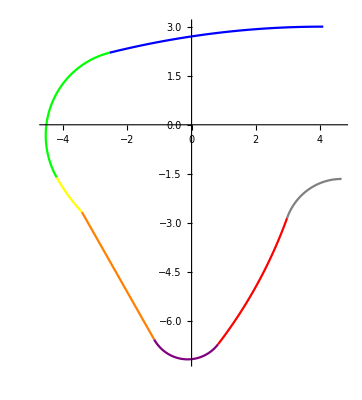

```mathematica
{t1A,t1B,t2B,t2C,t3C,t3D,t4D,t4E,t5E,t5F,t6F,t6G,t7G,t7H,y0}=ReadList["C:\\Users\\Jure\\OneDrive\\fakulteta\\5.semester\\diplomska\\python\\robne_vrednosti.txt",Number]

Show[
(*ListPlot[{{x1[t1A],y1[t1A]}, {x2[t2B], y2[t2B]}, {x3[t3C] ,y3[t3C]},{x4[t4D],y4[t4D]}, 
{x5[t5E], y5[t5E]},{x6[t6F],y6[t6F]}, {x7[t7G], y7[t7G]},{x7[t7H], y7[t7H]}}, PlotStyle->Red, PlotRange->{{-30,30},{-30,30}}],*)
ParametricPlot[{x1[t1], y1[t1]},{t1, t1A, t1B}, PlotStyle->Blue, PlotRange->All, AxesOrigin->{0,0} ],
ParametricPlot[{x2[t2], y2[t2]}, {t2, t2B,t2C}, PlotStyle->Green],
ParametricPlot[{x3[t3], y3[t3]}, {t3, t3C,t3D}, PlotStyle->Yellow],
ParametricPlot[{x4[t4], y4[t4]}, {t4, t4D,t4E}, PlotStyle->Orange],
ParametricPlot[{x5[t5], y5[t5]},{t5, t5E, t5F}, PlotStyle->Purple],
ParametricPlot[{x6[t6], y6[t6]}, {t6, t6F,t6G}, PlotStyle->Red],
ParametricPlot[{x7[t7], y7[t7]}, {t7, t7G,t7H}, PlotStyle->Gray],
AspectRatio->Full
]
```